```mathematica
Clear[a];
(*Plot3D[Exp[-a Sin[x+t]], {x,-1,1},{t,0,3}]*)
(*Manipulate[Plot3D[Exp[c]Exp[a Sin[ArcTan[x]-ArcTan[t]+ϕ]]/(Exp[c]Exp[a Sin[ArcTan[x]-ArcTan[t]+ϕ]]+Exp[b]), {x,-2,2},{t,0,4}],{a,-10,10},{b,-10,10},{c,-10,10},{ϕ,0,2Pi}]*)
Manipulate[Plot3D[Exp[c]Exp[a Sin[ArcTan[x]+ϕ]]/(Exp[c]Exp[a Sin[ArcTan[x]+ϕ]]+Exp[b]), {x,-2,2},{t,0,4}],{a,-10,10},{b,-10,10},{c,-10,10},{ϕ,0,2Pi}]
```

```mathematica
data={{0,0,1/2},{1,1,1/2},{1,-1,1/2},{2,2,1/2},{2,0,1/2},{2,-2,1/2},{3,3,0},{3,1,1/2},{3,-1,1/2},{3,-3,1},
{4,2,0},{4,0,1/2},{4,-2,1},{5,1,0},{5,-1,1}};
ListPlot3D[data,PlotRange->All]
```

-Graphics3D-

```mathematica
Clear[a];
Clear[b];
Clear[c];
FindFit[data,Exp[a]Exp[b Sin[x+t+ϕ1]]Exp[c Sin[x-t+ϕ2]]/(Exp[a]Exp[b Sin[x+t+ϕ1]]Exp[c Sin[x-t+ϕ2]]+Exp[d]),{a,b,c,d,ϕ1,ϕ2},{t,x}]
```

{a→-75.4515,b→-0.755745,c→0.755745,d→-75.4515,ϕ1→2.01198,ϕ2→1.12961}

```mathematica
a=-75.4515183483589;
b=-0.7557446471105963;
c=0.7557446471436257;
d=-75.45151834836956;
ϕ1=2.011984471205294;
ϕ2=1.129608182324843;
Plot3D[Exp[a]Exp[b Sin[x+t+ϕ1]]Exp[c Sin[x-t+ϕ2]]/(Exp[a]Exp[b Sin[x+t+ϕ1]]Exp[c Sin[x-t+ϕ2]]+Exp[d]),{t,0,5},{x,-3,3}]
```

-Graphics3D-

```mathematica
Import["1Qubit_T=20_final_policy_probabilities.csv"]
```

{{t,x,probability of action_0,probability of action_1},{0,0,0.185653,0.814347},{1,-1,0.908522,0.0914777},{1,1,0.0518588,0.948141},{2,-2,0.0869449,0.913055},{2,0,0.376048,0.623952},{2,2,0.994455,0.00554463},{3,-3,0.974874,0.0251265},{3,-1,0.0199626,0.980037},{3,1,0.735635,0.264365},{3,3,0.00774907,0.992251},{4,-4,0.023706,0.976294},{4,-2,0.0840235,0.915977},{4,0,0.722889,0.277111},{4,2,0.981993,0.018007},{4,4,0.989416,0.0105843},{5,-5,0.989033,0.0109671},{5,-3,0.00504547,0.994955},{5,-1,0.88891,0.11109},{5,1,0.789777,0.210223},{5,3,0.983281,0.0167192},{5,5,0.105341,0.894659},{6,-6,0.00721064,0.992789},{6,-4,0.0958913,0.904109},{6,-2,0.0128431,0.987157},{6,0,0.492783,0.507217},{6,2,0.972041,0.0279591},{6,4,0.957496,0.0425036},{6,6,0.952436,0.0475646},{7,-7,0.279628,0.720372},{7,-5,0.869118,0.130882},{7,-3,0.973836,0.0261638},{7,-1,0.47239,0.52761},{7,1,0.0367316,0.963268},{7,3,0.0109552,0.989045},{7,5,0.0450287,0.954971},{7,7,0.826249,0.173751},{8,-8,0.990199,0.00980067},{8,-6,0.00961613,0.990384},{8,-4,0.154886,0.845114},{8,-2,0.033048,0.966952},{8,0,0.0592955,0.940704},{8,2,0.91982,0.0801801},{8,4,0.704542,0.295458},{8,6,0.968168,0.0318323},{8,8,0.00500374,0.994996},{9,-9,0.488489,0.511511},{9,-7,0.420155,0.579845},{9,-5,0.00743031,0.99257},{9,-3,0.277155,0.722845},{9,-1,0.0970438,0.902956},{9,1,0.966151,0.0338491},{9,3,0.93298,0.0670201},{9,5,0.988269,0.0117313},{9,7,0.131228,0.868772},{9,9,0.0442999,0.9557},{10,-10,0.865009,0.134991},{10,-8,0.836035,0.163965},{10,-6,0.962403,0.0375973},{10,-4,0.108662,0.891339},{10,-2,0.0424304,0.95757},{10,0,0.482272,0.517728},{10,2,0.994975,0.00502531},{10,4,0.26293,0.73707},{10,6,0.174068,0.825932},{10,8,0.0153492,0.984651},{10,10,0.979817,0.0201832},{11,-11,0.661624,0.338376},{11,-9,0.980565,0.0194348},{11,-7,0.980478,0.0195222},{11,-5,0.988527,0.0114733},{11,-3,0.0273587,0.972641},{11,-1,0.960259,0.0397409},{11,1,0.163757,0.836243},{11,3,0.976852,0.0231482},{11,5,0.00758703,0.992413},{11,7,0.821875,0.178125},{11,9,0.852936,0.147064},{11,11,0.162714,0.837286},{12,-12,0.303485,0.696515},{12,-10,0.367021,0.632979},{12,-8,0.0186367,0.981363},{12,-6,0.010998,0.989002},{12,-4,0.00596951,0.99403},{12,-2,0.0776359,0.922364},{12,0,0.580641,0.419359},{12,2,0.986095,0.0139049},{12,4,0.933867,0.0661332},{12,6,0.790081,0.209919},{12,8,0.0270709,0.972929},{12,10,0.009731,0.990269},{12,12,0.00789728,0.992103},{13,-13,0.993139,0.00686058},{13,-11,0.178452,0.821548},{13,-9,0.168409,0.831591},{13,-7,0.0544287,0.945571},{13,-5,0.00925987,0.99074},{13,-3,0.994764,0.00523653},{13,-1,0.0345773,0.965423},{13,1,0.290784,0.709217},{13,3,0.00661324,0.993387},{13,5,0.899009,0.100991},{13,7,0.946142,0.0538577},{13,9,0.766153,0.233847},{13,11,0.950185,0.0498152},{13,13,0.0217919,0.978208},{14,-14,0.314782,0.685218},{14,-12,0.978372,0.0216283},{14,-10,0.811393,0.188607},{14,-8,0.491337,0.508663},{14,-6,0.0110778,0.988922},{14,-4,0.0707944,0.929206},{14,-2,0.080522,0.919478},{14,0,0.358598,0.641402},{14,2,0.934073,0.0659273},{14,4,0.986458,0.0135423},{14,6,0.92963,0.07037},{14,8,0.0812251,0.918775},{14,10,0.0231654,0.976835},{14,12,0.11036,0.88964},{14,14,0.0951225,0.904878},{15,-15,0.993351,0.00664903},{15,-13,0.8798,0.1202},{15,-11,0.986554,0.013446},{15,-9,0.904753,0.0952471},{15,-7,0.931491,0.068509},{15,-5,0.843737,0.156263},{15,-3,0.010684,0.989316},{15,-1,0.69244,0.30756},{15,1,0.947617,0.0523834},{15,3,0.985249,0.0147514},{15,5,0.569598,0.430402},{15,7,0.0168301,0.98317},{15,9,0.428446,0.571554},{15,11,0.960469,0.0395314},{15,13,0.895536,0.104464},{15,15,0.980606,0.0193945},{16,-16,0.00807912,0.991921},{16,-14,0.85164,0.14836},{16,-12,0.0687956,0.931204},{16,-10,0.00606631,0.993934},{16,-8,0.840546,0.159454},{16,-6,0.133825,0.866175},{16,-4,0.252858,0.747142},{16,-2,0.00675671,0.993243},{16,0,0.355766,0.644234},{16,2,0.986106,0.0138941},{16,4,0.422684,0.577316},{16,6,0.51641,0.48359},{16,8,0.969706,0.0302941},{16,10,0.0601704,0.93983},{16,12,0.972286,0.0277144},{16,14,0.204363,0.795637},{16,16,0.912525,0.0874755},{17,-17,0.0905915,0.909409},{17,-15,0.00490762,0.995092},{17,-13,0.0270306,0.97297},{17,-11,0.0743504,0.92565},{17,-9,0.822579,0.177421},{17,-7,0.680738,0.319262},{17,-5,0.989717,0.0102827},{17,-3,0.663577,0.336423},{17,-1,0.709161,0.290839},{17,1,0.0291009,0.970899},{17,3,0.024451,0.975549},{17,5,0.00779354,0.992207},{17,7,0.37496,0.62504},{17,9,0.533123,0.466877},{17,11,0.989904,0.0100958},{17,13,0.855328,0.144672},{17,15,0.878862,0.121138},{17,17,0.170004,0.829996},{18,-18,0.991564,0.00843566},{18,-16,0.889467,0.110533},{18,-14,0.0530452,0.946955},{18,-12,0.039419,0.960581},{18,-10,0.0258982,0.974102},{18,-8,0.986567,0.0134328},{18,-6,0.0106253,0.989375},{18,-4,0.0458051,0.954195},{18,-2,0.0510092,0.948991},{18,0,0.0914591,0.908541},{18,2,0.990276,0.00972362},{18,4,0.541007,0.458993},{18,6,0.695572,0.304428},{18,8,0.00627054,0.99373},{18,10,0.53618,0.46382},{18,12,0.943657,0.0563431},{18,14,0.930559,0.0694411},{18,16,0.0686258,0.931374},{18,18,0.178359,0.821641},{19,-19,0.0297136,0.970286},{19,-17,0.0877317,0.912268},{19,-15,0.529989,0.470011},{19,-13,0.0503059,0.949694},{19,-11,0.977636,0.0223638},{19,-9,0.0151144,0.984886},{19,-7,0.154654,0.845346},{19,-5,0.00493381,0.995066},{19,-3,0.904151,0.0958491},{19,-1,0.0282377,0.971762},{19,1,0.918256,0.0817441},{19,3,0.159768,0.840232},{19,5,0.995093,0.00490678},{19,7,0.0303326,0.969667},{19,9,0.140341,0.85966},{19,11,0.304803,0.695197},{19,13,0.0367922,0.963208},{19,15,0.986671,0.0133288},{19,17,0.972674,0.0273257},{19,19,0.971551,0.0284486}}

```mathematica
data={
{0,0,1/2},
{1,1,1/2},{1,-1,1/2},
{2,2,1/2},{2,0,1/2},{2,-2,1/2},
{3,3,1/2},{3,1,1/2},{3,-1,1/2},{3,-3,1/2},
{4,4,1/2},{4,2,1/2},{4,0,1/2},{4,-2,1/2},{4,-4,1/2},
{5,5,1/2},{5,3,1/2},{5,1,1/2},{5,-1,1/2},{5,-3,1/2},{5,-5,1/2},
{6,6,1/2},{6,4,1/2},{6,2,1/2},{6,0,1/2},{6,-2,1/2},{6,-4,1/2},{6,-6,1/2},
{7,7,1/2},{7,5,1/2},{7,3,1/2},{7,1,1/2},{7,-1,1/2},{7,-3,1/2},{7,-5,1/2},{7,-7,1/2},
{8,8,1/2},{8,6,1/2},{8,4,1/2},{8,2,1/2},{8,0,1/2},{8,-2,1/2},{8,-4,1/2},{8,-6,1/2},{8,-8,1/2},
{9,9,1/2},{9,7,1/2},{9,5,1/2},{9,3,1/2},{9,1,1/2},{9,-1,1/2},{9,-3,1/2},{9,-5,1/2},{9,-7,1/2},{9,-9,1/2},
{10,10,1},{10,8,1/2},{10,6,1/2},{10,4,1/2},{10,2,1/2},{10,0,1/2},{10,-2,1/2},{10,-4,1/2},{10,-6,1/2},{10,-8,1/2},{10,-10,0},
{11,9,1},{11,7,1/2},{11,5,1/2},{11,3,1/2},{11,1,1/2},{11,-1,1/2},{11,-3,1/2},{11,-5,1/2},{11,-7,1/2},{11,-9,0},
{12,8,1},{12,6,1/2},{12,4,1/2},{12,2,1/2},{12,0,1/2},{12,-2,1/2},{12,-4,1/2},{12,-6,1/2},{12,-8,0},
{13,7,1},{13,5,1/2},{13,3,1/2},{13,1,1/2},{13,-1,1/2},{13,-3,1/2},{13,-5,1/2},{13,-7,0},
{14,6,1},{14,4,1/2},{14,2,1/2},{14,0,1/2},{14,-2,1/2},{14,-4,1/2},{14,-6,0},
{15,5,1},{15,3,1/2},{15,1,1/2},{15,-1,1/2},{15,-3,1/2},{15,-5,0},
{16,4,1},{16,2,1/2},{16,0,1/2},{16,-2,1/2},{16,-4,0},
{17,3,1},{17,1,1/2},{17,-1,1/2},{17,-3,0},
{18,2,1},{18,0,1/2},{18,-2,0},
{19,1,1},{19,-1,0}};
importeddata={
{0,0,0.18565328},{1,-1,0.9085223},{1,1,0.05185875},{2,-2,0.086944915},{2,0,0.3760483},{2,2,0.9944554},{3,-3,0.9748735},{3,-1,0.019962648},{3,1,0.73563516},{3,3,0.007749073},{4,-4,0.023706032},{4,-2,0.084023476},{4,0,0.7228889},{4,2,0.98199296},{4,4,0.98941576},{5,-5,0.98903286},{5,-3,0.005045474},{5,-1,0.8889103},{5,1,0.7897774},{5,3,0.98328084},{5,5,0.10534104},{6,-6,0.007210641},{6,-4,0.09589133},{6,-2,0.012843099},{6,0,0.49278295},{6,2,0.9720409},{6,4,0.95749635},{6,6,0.9524355},{7,-7,0.27962765},{7,-5,0.86911786},{7,-3,0.97383624},{7,-1,0.47239015},{7,1,0.036731634},{7,3,0.010955165},{7,5,0.045028657},{7,7,0.826249},{8,-8,0.99019927},{8,-6,0.00961613},{8,-4,0.15488623},{8,-2,0.033047955},{8,0,0.0592955},{8,2,0.91981995},{8,4,0.7045423},{8,6,0.9681677},{8,8,0.0050037415},{9,-9,0.48848867},{9,-7,0.42015544},{9,-5,0.00743031},{9,-3,0.27715525},{9,-1,0.09704375},{9,1,0.9661509},{9,3,0.9329799},{9,5,0.9882686},{9,7,0.13122785},{9,9,0.04429991},
{10,-10,0.86500865},{10,-8,0.83603543},{10,-6,0.9624027},{10,-4,0.1086615},{10,-2,0.04243042},{10,0,0.4822719},{10,2,0.99497473},{10,4,0.26292977},{10,6,0.17406788},{10,8,0.015349204},{10,10,0.97981685},
{11,-9,0.98056525},{11,-7,0.98047775},{11,-5,0.9885266},{11,-3,0.027358718},{11,-1,0.9602591},{11,1,0.16375677},{11,3,0.9768519},{11,5,0.0075870296},{11,7,0.8218746},{11,9,0.85293627},
{12,-8,0.018636664},{12,-6,0.010998021},{12,-4,0.0059695113},{12,-2,0.077635884},{12,0,0.58064145},{12,2,0.9860952},{12,4,0.9338668},{12,6,0.79008126},{12,8,0.027070884},
{13,-7,0.054428708},{13,-5,0.009259874},{13,-3,0.9947635},{13,-1,0.03457727},{13,1,0.29078355},{13,3,0.0066132434},{13,5,0.8990093},{13,7,0.94614226},
{14,-6,0.011077811},{14,-4,0.070794396},{14,-2,0.08052198},{14,0,0.35859776},{14,2,0.9340727},{14,4,0.98645777},{14,6,0.92963004},
{15,-5,0.8437374},{15,-3,0.010683961},{15,-1,0.69244045},{15,1,0.9476166},{15,3,0.9852486},{15,5,0.5695984},
{16,-4,0.25285828},{16,-2,0.0067567113},{16,0,0.35576645},{16,2,0.9861058},{16,4,0.4226838},
{17,-3,0.66357684},{17,-1,0.7091608},{17,1,0.029100886},{17,3,0.024450986},
{18,-2,0.05100922},{18,0,0.09145912},{18,2,0.99027634},
{19,-1,0.028237665},{19,1,0.91825587}};
ListPlot3D[{data,importeddata},PlotRange->All]
```

-Graphics3D-

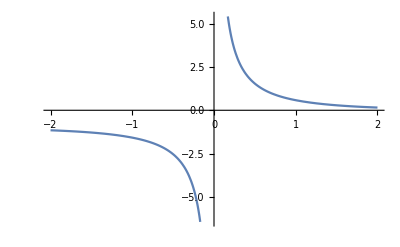

```mathematica
Plot[1/(Exp[x]-1),{x,-2,2}]
```

```mathematica
RY[theta_]:={{},{}}+{{},{}};
RZ[theta_]:={{},{}}+{{},{}};
VX=1/Sqrt[2]*{{1,1},{1,-1}};
VXdagger=VX;
Z={{1,0},{0,-1}};
akj =Conjugate[VXdagger[[1]][[j4]]]*Conjugate[VX[[j6]][[j5]]*RY[theta4][[ip]][[j7]]]* Conjugate[RZ[theta4][[ip]][[j7]]* Conjugate[VXdagger[[j5]][[j4]]*VX[[j6]][[j5]]*Conjugate[RY[theta4][[ip]][[j7]]*Conjugate[ RZ[theta4][[ip]][[j7]]* Z[[i]][[ip]]*RZ[theta4][[ip]][[j7]]* RY[theta3][[j7]][[j6]]*VX[[j6]][[j5]]*VXdagger[[j5]][[j4]]*RZ[theta2][[j4]][[j3]]* RY[theta1][[j3]][[j2]]*VX[[j2]][[j1]]*VXdagger[[j1]][[1]]
```

```mathematica
ClearAll[a,ax,at,axpt,axmt,ϕx,ϕt,ϕxpt,ϕxmt,λx,λt];
gx[x_]:=ArcTan[λx*x];
gt[t_]:=ArcTan[λt*t];
f[t_,x_]:=a+ax*Sin[gx[x]+ϕx]+at*Sin[gt[t]+ϕt]+axpt*Sin[gx[x]+gt[t]+ϕxpt]+axmt*Sin[gx[x]-gt[t]+ϕxmt];

FindFit[
data,
1/(Exp[f[t,x]]+1),{a,ax,at,axpt,axmt,ϕx,ϕt,ϕxpt,ϕxmt,λx,λt},{t,x}]
NonlinearModelFit[
data,
1/(Exp[f[t,x]]+1),{a,ax,at,axpt,axmt,ϕx,ϕt,ϕxpt,ϕxmt,λx,λt},{t,x}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→0.133903,ax→-10.7672,at→-0.136393,axpt→15.4468,axmt→-15.3099,ϕx→0.0137014,ϕt→1.47576,ϕxpt→1.04502,ϕxmt→2.10057,λx→0.0527407,λt→0.0237204}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[1/(1+ⅇ^(«7»+15.4468 Sin[«1»]))]

```mathematica
data={
{0,0,1/2},
{1,1,1/2},{1,-1,1/2},
{2,2,1/2},{2,0,1/2},{2,-2,1/2},
{3,3,1/2},{3,1,1/2},{3,-1,1/2},{3,-3,1/2},
{4,4,1/2},{4,2,1/2},{4,0,1/2},{4,-2,1/2},{4,-4,1/2},
{5,5,1/2},{5,3,1/2},{5,1,1/2},{5,-1,1/2},{5,-3,1/2},{5,-5,1/2},
{6,6,1/2},{6,4,1/2},{6,2,1/2},{6,0,1/2},{6,-2,1/2},{6,-4,1/2},{6,-6,1/2},
{7,7,1/2},{7,5,1/2},{7,3,1/2},{7,1,1/2},{7,-1,1/2},{7,-3,1/2},{7,-5,1/2},{7,-7,1/2},
{8,8,1/2},{8,6,1/2},{8,4,1/2},{8,2,1/2},{8,0,1/2},{8,-2,1/2},{8,-4,1/2},{8,-6,1/2},{8,-8,1/2},
{9,9,1/2},{9,7,1/2},{9,5,1/2},{9,3,1/2},{9,1,1/2},{9,-1,1/2},{9,-3,1/2},{9,-5,1/2},{9,-7,1/2},{9,-9,1/2},
{10,10,1},{10,8,1/2},{10,6,1/2},{10,4,1/2},{10,2,1/2},{10,0,1/2},{10,-2,1/2},{10,-4,1/2},{10,-6,1/2},{10,-8,1/2},{10,-10,0},
{11,9,1},{11,7,1/2},{11,5,1/2},{11,3,1/2},{11,1,1/2},{11,-1,1/2},{11,-3,1/2},{11,-5,1/2},{11,-7,1/2},{11,-9,0},
{12,8,1},{12,6,1/2},{12,4,1/2},{12,2,1/2},{12,0,1/2},{12,-2,1/2},{12,-4,1/2},{12,-6,1/2},{12,-8,0},
{13,7,1},{13,5,1/2},{13,3,1/2},{13,1,1/2},{13,-1,1/2},{13,-3,1/2},{13,-5,1/2},{13,-7,0},
{14,6,1},{14,4,1/2},{14,2,1/2},{14,0,1/2},{14,-2,1/2},{14,-4,1/2},{14,-6,0},
{15,5,1},{15,3,1/2},{15,1,1/2},{15,-1,1/2},{15,-3,1/2},{15,-5,0},
{16,4,1},{16,2,1/2},{16,0,1/2},{16,-2,1/2},{16,-4,0},
{17,3,1},{17,1,1/2},{17,-1,1/2},{17,-3,0},
{18,2,1},{18,0,1/2},{18,-2,0},
{19,1,1},{19,-1,0}};
plot1=ListPlot3D[data,PlotRange->All,PlotStyle->{Green,Opacity[0.6]}]

a=0.13390266552073662;
ax=-10.7671724001222;at=-0.1363925776176785;axpt=15.446813753051861;axmt=-15.309933726741729;ϕx=0.013701409001938876;ϕt=1.4757614404304402;ϕxpt=1.0450188947001662;ϕxmt=2.100570327571774;λx=0.05274068000450396;λt=0.023720361214886576;

plot2=Plot3D[1/(Exp[f[t,x]]+1),{t,0,19},{x,-10,10},PlotStyle->{Blue,Opacity[0.6]}]
Show[plot1,plot2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-